```mathematica
$Assumptions={Element[{r,c, Ω,z',z},Reals],r>0,c>0, Ω > 0,z'>0, z>0};
```

```mathematica
expr1 = 1/4/π μ Integrate[I0/(π a^2) r/(r^2+(z-z')^2)^(3/2) r' , {θ, 0, 2π},{r', 0, a} , {z', -Infinity, Infinity}]
expr2 = 1/4/π μ Integrate[I0/(π a^2) r/(r^2+(z-z')^2) r' , {θ, 0, 2π},{r', 0, a} , {z', -Infinity, Infinity}]
```

(I0 μ)/(2 π r)

(I0 μ)/4

```mathematica
prefactor =1/4/π μ 2π I0 a^2/2 /(π a^2) 2
Bint1 = prefactor Integrate[r/u^2/Sqrt[u^2-r^2]Cos[Ω (t-u/c)], {u, r, Infinity}]
```

(I0 μ)/(2 π)

1/8 I0 μ ((2 Cos[t Ω] MeijerG[{{},{3/2}},{{0,1},{1/2}},(r^2 Ω^2)/(4 c^2)])/r+1/c^2 Ω Sin[t Ω] (2 c-2 r Ω BesselJ[0,(r Ω)/c]+2 c BesselJ[1,(r Ω)/c]-π r Ω BesselJ[1,(r Ω)/c] StruveH[0,(r Ω)/c]+π r Ω BesselJ[0,(r Ω)/c] StruveH[1,(r Ω)/c]))

```mathematica
FullSimplify[Series[Bint1, {c, Infinity, 1}]]
```

(I0 μ Cos[t Ω])/(2 π r)+(I0 μ Ω Sin[t Ω])/(4 c)+O[1/c]^2

```mathematica
Bint2 = prefactor Integrate[r/Sqrt[u^2-r^2] /u Sin[Ω (t-u/c)], {u,r, Infinity}]
```

(I0 μ ∫_r^∞ (r Sin[(t-u/c) Ω])/(u √(-r^2+u^2))ⅆu)/(2 π)

```mathematica
Bint21 = prefactor Integrate[r/Sqrt[u^2-r^2] /u Cos[Ω (u/c)], {u,r, Infinity}]/c Ω
```

(I0 μ Ω (2 c-π r Ω BesselJ[1,(r Ω)/c] StruveH[0,(r Ω)/c]+r Ω BesselJ[0,(r Ω)/c] (-2+π StruveH[1,(r Ω)/c])))/(8 c^2)

```mathematica
FullSimplify[Series[Bint21, {c, Infinity, 1}]]
```

(I0 μ Ω)/(4 c)+O[1/c]^2

```mathematica
Bint21 = prefactor Integrate[1/Sqrt[u^2-r^2] /u Sin[Ω (u/c)], {u,r, Infinity}]/c Ω r
```

(I0 r μ Ω ∫_r^∞ Sin[(u Ω)/c]/(u √(-r^2+u^2))ⅆu)/(2 c π)

```mathematica
Integrate[1/Sqrt[u^2-r^2], {u,r,Infinity}]
```

Integrate::idiv: Integral of 1/(√(-r^2+u^2)) does not converge on {r,∞}.

∫_r^∞ 1/(√(-r^2+u^2))ⅆu

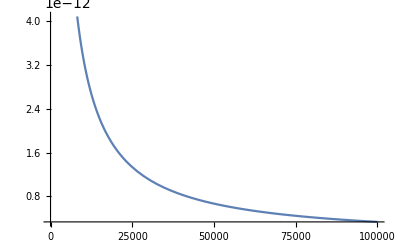

```mathematica
Plot[1/Sqrt[u^2-1^2]/u Sin[u/c] /. {c-> 30000000},{u,1, 100000}]
```